```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[Subscript[a, 1]];
Clear[Subscript[a, 2]];
Clear[Subscript[a, 3]];
Clear[SuperPlus[Subscript[e, 12]]];
Clear[SuperMinus[Subscript[e, 12]]];
Clear[SuperPlus[Subscript[e, 23]]];
Clear[SuperMinus[Subscript[e, 23]]];
Clear[SuperPlus[Subscript[e, 13]]];
Clear[SuperMinus[Subscript[e, 13]]];
Clear[b1];
Clear[b2];
Clear[b3];
Clear[c1];
Clear[c2];
Clear[c3];
Clear[V1];
Clear[V2];
Clear[V3];
Clear[EntangledCounter1];
Clear[EntangledCounter2];
Clear[EntangledCounter3];
Clear[EntangledCounterTRI];
```

Clear::ssym: a_1 is not a symbol or a string.

Clear::ssym: a_2 is not a symbol or a string.

Clear::ssym: a_3 is not a symbol or a string.

Clear::ssym: (e_12)^+ is not a symbol or a string.

Clear::ssym: (e_12)^- is not a symbol or a string.

Clear::ssym: (e_23)^+ is not a symbol or a string.

Clear::ssym: (e_23)^- is not a symbol or a string.

Clear::ssym: (e_13)^+ is not a symbol or a string.

Clear::ssym: (e_13)^- is not a symbol or a string.

```mathematica
c1=Table[RandomReal[{1,20}],{i,10^5}];
c2=Table[RandomReal[{1,20}],{i,10^5}];
c3=Table[RandomReal[{1,20}],{i,10^5}];
(*The range of values for C seems to scale the bipartiton graphs at the end*)
```

```mathematica
a1=Table[c1[[i]]-1,{i,1,Length[c1]}];
a2=Table[c2[[i]]-1,{i,1,Length[c2]}];
a3=Table[c3[[i]]-1,{i,1,Length[c3]}];

(*these values a1,a2,a3 are all greater than 0*)

c1[[1]]
a1[[1]]
```

2.84784

1.84784

```mathematica
a1;
```

```mathematica
a2;
```

```mathematica
a3;
```

```mathematica
b1={};
b2={};
b3={};
```

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,Print[{i ,a1[[i]],a2[[i]],a3[[i]]}],Print["NO"]]
,{i,1,Length[a1]}];

(*Only currently evaluating the first inequality, need to refine the values of aj[[i]] more to include the second 2 inequalities also.*)
```

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,AppendTo[b1,a1[[i]]]&&AppendTo[b2,a2[[i]]]&&AppendTo[b3,a3[[i]]];]
,{i,1,Length[a1]}];
```

```mathematica
b1
```

```mathematica
b2;
```

```mathematica
b3;
```

```mathematica
Subscript[a, 1]=Table[b1[[i]]+1,{i,1,Length[b1]}];
Subscript[a, 2]=Table[b2[[i]]+1,{i,1,Length[b2]}];
Subscript[a, 3]=Table[b3[[i]]+1,{i,1,Length[b3]}];
```

```mathematica
Subscript[a, 1];
```

```mathematica
SuperPlus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))+√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))-√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
```

```mathematica
Subscript[σ, SF]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
Subscript[σ, SF][[1]]//MatrixForm
```

(16.3079 | 0 | 12.3862 | 0 | 15.3998 | 0
0 | 16.3079 | 0 | -5.73077 | 0 | -12.5953
12.3862 | 0 | 9.51454 | 0 | 11.708 | 0
0 | -5.73077 | 0 | 9.51454 | 0 | -1.58389
15.3998 | 0 | 11.708 | 0 | 14.612 | 0
0 | -12.5953 | 0 | -1.58389 | 0 | 14.612)

```mathematica
Eigenvalues[Subscript[σ, SF][[1]]]
```

{37.3286,22.8727,14.5416,0.0687682,0.0437203,0.0267891}

```mathematica
(*All eigenvalues now real and positive therefore we have physical states*)
```

```mathematica
Subscript[σ, PT1]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
(*Subscript[σ, PT1]=Subscript[P1σ, SF] P1 calculated by hand*)
```

```mathematica
Subscript[σ, PT1][[1]]
```

{{6.0374,0,6.81477,0,5.87162,0},{0,6.0374,0,4.55246,0,0.753834},{6.81477,0,7.91277,0,6.79311,0},{0,4.55246,0,7.91277,0,-4.50278},{5.87162,0,6.79311,0,6.00118,0},{0,0.753834,0,-4.50278,0,6.00118}}

```mathematica
Length[Subscript[σ, SF]]
```

49862

```mathematica
Subscript[σ, PT2]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
(*Subscript[σ, PT2]=Subscript[P2σ, SF] P2 calculated by hand*)
```

```mathematica
Subscript[σ, PT3]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
(*Subscript[σ, PT2]=Subscript[P2σ, SF] P2 calculated by hand*)
```

```mathematica
zero={{0,0},{0,0}};
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero,zero},{zero,ⅈ PauliMatrix[2],zero},{zero,zero,ⅈ PauliMatrix[2]}}]
```

{{0,1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,-1,0}}

```mathematica
V1={};
Do[AppendTo[V1,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT1][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT1]]}]
```

```mathematica
V2={};
Do[AppendTo[V2,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT2][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT2]]}]
```

```mathematica
V3={};
Do[AppendTo[V3,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT3][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT3]]}]
```

```mathematica
Table[{i,V1[[i]]},{i,1,Length[V1]}];
Table[{i,V2[[i]]},{i,1,Length[V2]}];
Table[{i,V3[[i]]},{i,1,Length[V3]}];
```

```mathematica
Max[Table[V1[[i]],{i,1,Length[V1]}]]
Max[Table[V2[[i]],{i,1,Length[V1]}]]
Max[Table[V3[[i]],{i,1,Length[V1]}]]
```

0.806606

0.654317

0.701014

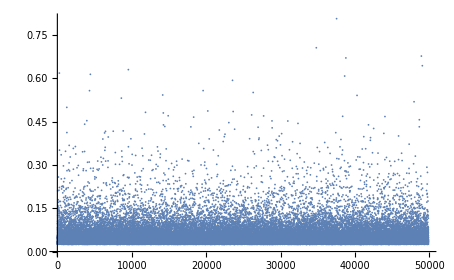

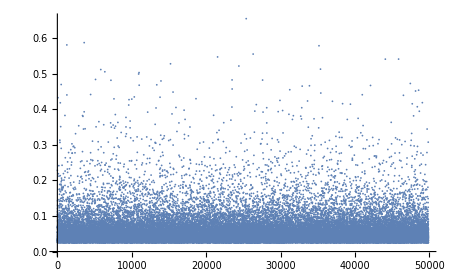

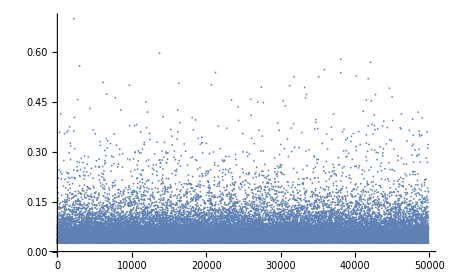

```mathematica
ListPlot[Table[{i,V1[[i]]},{i,1,Length[V1]}],PlotRange->All]
ListPlot[Table[{i,V2[[i]]},{i,1,Length[V2]}],PlotRange->All]
ListPlot[Table[{i,V3[[i]]},{i,1,Length[V3]}],PlotRange->All]
```

```mathematica
(*The values on the Y-axis scale along with the range of values at the very start initially chosen for c
i.e. if I chose values between 1 and 10 then the points converge to 1/(2(upper limit)) i.e. to 0.05 *)

EntangledCounter1={};
Do[If[V1[[i]]<1
,AppendTo[EntangledCounter1,V1[[i]]];]
,{i,1,Length[V1]}];
Length[EntangledCounter1]
(*Points that are entangled from mode 1*)
```

49862

```mathematica
EntangledCounter2={};
Do[If[V2[[i]]<1
,AppendTo[EntangledCounter2,V2[[i]]];]
,{i,1,Length[V2]}];
Length[EntangledCounter2]
(*Points that are entangled from mode 2*)
```

316

```mathematica
EntangledCounter3={};
Do[If[V3[[i]]<1
,AppendTo[EntangledCounter3,V3[[i]]];]
,{i,1,Length[V3]}];
Length[EntangledCounter3]
(*Points that are entangled from mode 3*)
```

190

```mathematica
EntangledCounterTRI={};
Do[If[V1[[i]]<1&&V2[[i]]<1&&V3[[i]]<1
,AppendTo[EntangledCounterTRI,V1[[i]]]&&AppendTo[EntangledCounterTRI,V2[[i]]]&&AppendTo[EntangledCounterTRI,V3[[i]]];]
,{i,1,Length[V1]}];
Length[EntangledCounterTRI]/3
(*Points that are tripartite entangled*)
```

78

```mathematica
Ratio=Length[EntangledCounterTRI]/(3Length[Subscript[σ, SF]])
(*Ratio of number of tripartite entangled points to the number of physically significant states*)
```

1